```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
FinancialChart[symbols_,start_,end_,weightList_:Nothing]:=Module[{lists,allDates,ruleLists,listsWithMissing,mean,weighted,data,table,ts,headings},
lists=NormalizeData[#,start,end]&/@symbols;
allDates=Table[#1&@@i,{stock,lists},{i,stock}]//Fold[Union,#]&;
ruleLists=Table[#1->#2&@@i,{stock,lists},{i,stock}];
listsWithMissing=Table[Module[{association},
association=Association@a;
Table[k->association[k],{k,allDates}]],{a,ruleLists}];
mean=If[Length@symbols>1,Normal@Merge[listsWithMissing,Mean],Nothing];
weighted=If[TrueQ[weightList==Nothing],Nothing,Normal@Merge[listsWithMissing,Total[#*weightList]&]];
data=listsWithMissing~Join~{mean,weighted};
table=Table[Select[Values@d,NumberQ]//{Last@#,StandardDeviation@#}&//{#1,#2,#1/#2}&@@#&,{d,data}];
ts=Transpose@{Keys@#,Values@#}&/@data;
headings=symbols~Join~{If[Length@symbols>1,"Mean",Nothing],If[TrueQ[weightList==Nothing],Nothing,"Weighted Mean"]};
TableForm@{DateListPlot[ts,PlotLegends->headings,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],TableForm[table,TableHeadings->{headings,{"Return","Standard Deviation","Return/SD"}}]}
]
```

{{AMZN,MSFT,V,BA,MA,JPM,CSCO,INTC,NFLX,ADBE},{5.50492,5.42186,4.9617,4.76633,4.55376,4.37947,3.69114,3.49097,3.36582,2.99286}}

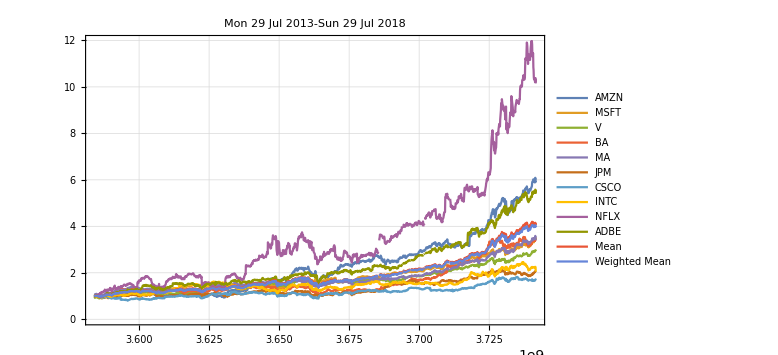
-Graphics-
 | Return | Standard Deviation | Return/SD
AMZN | 5.93685 | 1.28334 | 4.6261
MSFT | 3.41408 | 0.589292 | 5.79353
V | 2.93192 | 0.498502 | 5.88145
BA | 3.44099 | 0.685458 | 5.01999
MA | 3.39922 | 0.577349 | 5.88763
JPM | 2.0835 | 0.343896 | 6.05851
CSCO | 1.68062 | 0.238414 | 7.04914
INTC | 2.05164 | 0.325738 | 6.29842
NFLX | 10.1505 | 2.38485 | 4.25625
ADBE | 5.40195 | 1.11533 | 4.84336
Mean | 4.04913 | 0.789282 | 5.13014
Weighted Mean | 3.95193 | 0.762617 | 5.18207

```mathematica
{symbols,weights}=ImportString[StringDrop[Import["https://www.ishares.com/us/products/251614/ishares-msci-usa-momentum-factor-etf/1467271812596.ajax?tab=top&fileType=json","String"],3],"JSON"]//Transpose@Table[{i[[1]],i[[6,2,2]]},{i,#[[1,2]]}]&
weights=weights/Total@weights;
start=DatePlus[Today,-Quantity[5, "Years"]];
end=Today;
topChart=FinancialChart[symbols,start,end,weights]
Export[FileNameJoin[{NotebookDirectory[],"topChart.svg"}],topChart];
```

{{AMZN,MSFT,V,BA,MA,JPM,CSCO,INTC,NFLX,ADBE,HD,NVDA,ABBV,NKE,ABT,COST,PYPL,VLO,TXN,ISRG,ACN,SPGI,INTU,CAT,SCHW,ZTS,PSX,EL,CME,RTN,PGR,ANTM,BLK,FOXA,SYK,RHT,NOC,NOW,MU,MAR,TROW,TGT,SQ,ROST,VFC,HCA,TWTR,NTAP,MCO,ABMD,PXD,ANDV,ALGN,YUM,FISV,ETFC,HFC,DG,FOX,MSCI,PANW,FLT,BR,VRSK,BBY,GWW,MSI,CPRT,CTAS,LULU,BFB,SIVB,HRS,HPE,CSGP,HLT,SPLK,RF,ANET,ANSS,TRU,TSS,IAC,XL,AMTD,GPN,STX,CTXS,MELI,GDDY,CXO,TPR,NKTR,KSS,PVH,CMA,XPO,XYL,CBRE,FFIV,KORS,NDAQ,CHRW,AKAM,SSNC,DPZ,FTNT,AJG,TFX,FANG,JKHY,VST,VOYA,JLL,BLKFDS,ODFL,IEX,FLIR,IPGP,SPR,FLR,CLR,ALV,WLK,USD,HP,SGAFT,ESU8},{5.50492,5.42186,4.9617,4.76633,4.55376,4.37947,3.69114,3.49097,3.36582,2.99286,2.76418,2.40614,1.75436,1.5052,1.42571,1.32104,1.30865,1.24557,1.17334,1.16862,1.14702,1.02918,1.01374,1.00352,0.96644,0.96541,0.92733,0.90381,0.90301,0.86426,0.85171,0.84476,0.83723,0.81714,0.733,0.71293,0.69503,0.6666,0.66143,0.64809,0.63367,0.59546,0.58777,0.53903,0.53027,0.48966,0.48551,0.48115,0.47485,0.45345,0.4459,0.4422,0.44151,0.41904,0.39584,0.36384,0.36117,0.36028,0.35971,0.34848,0.34743,0.34242,0.33466,0.33118,0.3277,0.31884,0.31741,0.31714,0.30872,0.3083,0.30074,0.29428,0.29148,0.29108,0.28998,0.28869,0.28276,0.2815,0.27528,0.27442,0.27243,0.26389,0.25946,0.25945,0.25751,0.24155,0.24117,0.24002,0.23838,0.23809,0.23758,0.23581,0.23248,0.23081,0.22233,0.22013,0.21146,0.198,0.19347,0.19059,0.18972,0.18776,0.18688,0.18277,0.18038,0.17613,0.17456,0.17226,0.16495,0.15347,0.13864,0.13707,0.13407,0.1313,0.1308,0.12849,0.12782,0.12718,0.11759,0.11358,0.10385,0.10375,0.09812,0.08255,0.06883,0.06796,0.00885,0}}

{{115},{125},{127},{128}}

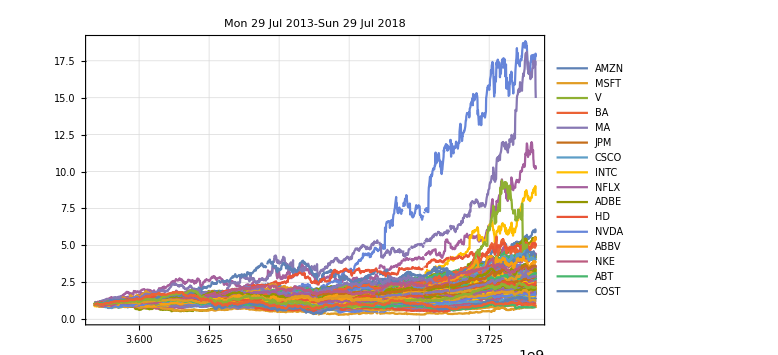
-Graphics-
 | Return | Standard Deviation | Return/SD
AMZN | 5.93685 | 1.28334 | 4.6261
MSFT | 3.41408 | 0.589292 | 5.79353
V | 2.93192 | 0.498502 | 5.88145
BA | 3.44099 | 0.685458 | 5.01999
MA | 3.39922 | 0.577349 | 5.88763
JPM | 2.0835 | 0.343896 | 6.05851
CSCO | 1.68062 | 0.238414 | 7.04914
INTC | 2.05164 | 0.325738 | 6.29842
NFLX | 10.1505 | 2.38485 | 4.25625
ADBE | 5.40195 | 1.11533 | 4.84336
HD | 2.50591 | 0.449611 | 5.5735
NVDA | 17.7855 | 5.57576 | 3.18978
ABBV | 2.00976 | 0.375417 | 5.35342
NKE | 2.45224 | 0.335782 | 7.30308
ABT | 1.77627 | 0.201459 | 8.81702
COST | 1.87511 | 0.214122 | 8.75717
PYPL | 2.32798 | 0.484304 | 4.80685
VLO | 3.25091 | 0.502434 | 6.47032
TXN | 2.91785 | 0.559709 | 5.21316
ISRG | 1.3279 | 0.422711 | 3.1414
ACN | 2.23877 | 0.361986 | 6.18469
SPGI | 3.4096 | 0.642676 | 5.30532
INTU | 3.34136 | 0.546666 | 6.11225
CAT | 1.71718 | 0.305458 | 5.62165
SCHW | 2.38972 | 0.439242 | 5.44057
ZTS | 2.83151 | 0.521277 | 5.43187
PSX | 2.01476 | 0.200563 | 10.0455
EL | 2.07258 | 0.339561 | 6.1037
CME | 2.22582 | 0.377038 | 5.90345
RTN | 2.76505 | 0.556034 | 4.9728
PGR | 2.30624 | 0.436911 | 5.27852
ANTM | 2.91653 | 0.522211 | 5.58497
BLK | 1.77635 | 0.265702 | 6.6855
FOXA | 1.50953 | 0.149886 | 10.0712
SYK | 2.40284 | 0.42504 | 5.65322
RHT | 2.86468 | 0.597334 | 4.79578
NOC | 3.30069 | 0.789546 | 4.18049
NOW | 4.20457 | 0.802394 | 5.24004
MU | 4.32719 | 0.982446 | 4.4045
MAR | 3.13843 | 0.664506 | 4.72295
TROW | 1.59467 | 0.186026 | 8.57229
TGT | 1.12054 | 0.122791 | 9.12562
SQ | 5.3443 | 1.29398 | 4.13013
ROST | 2.56163 | 0.440263 | 5.81841
VFC | 1.86618 | 0.181824 | 10.2637
HCA | 3.17926 | 0.415059 | 7.65977
TWTR | 0.759911 | 0.297191 | 2.55697
NTAP | 1.94444 | 0.296054 | 6.56787
MCO | 2.72868 | 0.432753 | 6.30539
ABMD | 14.9825 | 3.78032 | 3.9633
PXD | 1.20098 | 0.168607 | 7.12298
ANDV | 2.73341 | 0.412593 | 6.62495
ALGN | 8.35546 | 1.90763 | 4.38002
YUM | 1.49557 | 0.205462 | 7.27903
FISV | 1.64762 | 0.560412 | 2.94002
ETFC | 4.11492 | 0.8205 | 5.01513
HFC | 1.62363 | 0.245317 | 6.6185
DG | 1.79827 | 0.234776 | 7.65951
FOX | 1.49083 | 0.141284 | 10.552
MSCI | 4.92169 | 1.02379 | 4.80732
PANW | 4.26693 | 0.893827 | 4.77377
FLT | 2.47778 | 0.303272 | 8.17017
BR | 4.1136 | 0.77403 | 5.31453
VRSK | 1.82035 | 0.216164 | 8.42116
BBY | 2.58766 | 0.50127 | 5.16222
GWW | 1.31876 | 0.124987 | 10.5512
MSI | 2.28569 | 0.284224 | 8.04185
CPRT | 3.53665 | 0.702259 | 5.0361
CTAS | 4.37071 | 0.814061 | 5.36902
LULU | 1.73787 | 0.245483 | 7.07941
BFB | 1.48807 | 0.185501 | 8.02191
SIVB | 3.61948 | 0.666104 | 5.43381
HRS | 2.91274 | 0.552856 | 5.26853
HPE | 1.63053 | 0.2914 | 5.5955
CSGP | 2.69074 | 0.429076 | 6.27101
HLT | 1.72595 | 0.262481 | 6.57554
SPLK | 2.02768 | 0.330235 | 6.14011
RF | 1.84493 | 0.327194 | 5.63864
ANET | 4.93236 | 1.31255 | 3.75785
ANSS | 2.23684 | 0.362177 | 6.17609
TRU | 2.83701 | 0.564621 | 5.02462
TSS | 3.42968 | 0.658064 | 5.21177
IAC | 2.91194 | 0.610453 | 4.77012
XL | 1.75601 | 0.204314 | 8.59468
AMTD | 2.24082 | 0.346934 | 6.45893
GPN | 5.02288 | 1.1837 | 4.24339
STX | 1.35707 | 0.278217 | 4.87775
CTXS | 2.03981 | 0.307227 | 6.63941
MELI | 3.06668 | 0.714712 | 4.2908
GDDY | 2.93728 | 0.509524 | 5.76476
CXO | 1.68419 | 0.198685 | 8.47668
TPR | 0.822299 | 0.120082 | 6.84781
NKTR | 4.37868 | 1.88847 | 2.31864
KSS | 1.36035 | 0.195821 | 6.94687
PVH | 1.16763 | 0.150727 | 7.74662
CMA | 2.29153 | 0.431313 | 5.31291
XPO | 3.99757 | 0.971089 | 4.11658
XYL | 2.46627 | 0.480507 | 5.13264
CBRE | 2.104 | 0.265424 | 7.92693
FFIV | 2.00726 | 0.238666 | 8.41032
KORS | 1.04234 | 0.272274 | 3.82829
NDAQ | 2.89852 | 0.504222 | 5.74849
CHRW | 1.5479 | 0.166854 | 9.27699
AKAM | 1.70353 | 0.20571 | 8.28121
SSNC | 3.05892 | 0.519785 | 5.88497
DPZ | 4.21299 | 0.927338 | 4.54311
FTNT | 3.23073 | 0.526714 | 6.13375
AJG | 1.62405 | 0.190501 | 8.52519
TFX | 3.46188 | 0.731372 | 4.7334
FANG | 3.51314 | 0.608236 | 5.77595
JKHY | 2.86229 | 0.479263 | 5.97228
VST | 1.39688 | 0.175634 | 7.95331
VOYA | 1.67368 | 0.22534 | 7.42736
JLL | 1.82574 | 0.277077 | 6.58929
ODFL | 3.29176 | 0.665674 | 4.94501
IEX | 2.53851 | 0.402576 | 6.30568
FLIR | 1.84886 | 0.224633 | 8.23057
IPGP | 3.84059 | 0.956324 | 4.01599
SPR | 3.68579 | 0.746862 | 4.93504
FLR | 0.835821 | 0.18841 | 4.43618
CLR | 1.33136 | 0.292993 | 4.54402
ALV | 1.25403 | 0.197737 | 6.34189
WLK | 2.10681 | 0.403467 | 5.22176
HP | 0.958859 | 0.265476 | 3.61185
Mean | 2.88055 | 0.431715 | 6.67233
Weighted Mean | 3.55926 | 0.571843 | 6.22418

```mathematica
{symbols0,weights0}=ImportString[StringDrop[Import["https://www.ishares.com/us/products/251614/ishares-msci-usa-momentum-factor-etf/1467271812596.ajax?tab=all&fileType=json","String"],3],"JSON"]//Transpose@Table[{i[[1]],i[[4,2,2]]},{i,#[[1,2]]}]&
weights0=weights0/100;
indices=Flatten@Join[Position[StringMatchQ[symbols0,#],True]&/@{"BLKFDS","USD","SGAFT"},Position[StringContainsQ[symbols0,"ES"],True]]//Partition[#,1]&
{symbols0,weights0}={Delete[symbols0,indices],Delete[weights0,indices]};
allChart=FinancialChart[symbols0,start,end,weights0]
Export[FileNameJoin[{NotebookDirectory[],"allChart.svg"}],allChart];
```

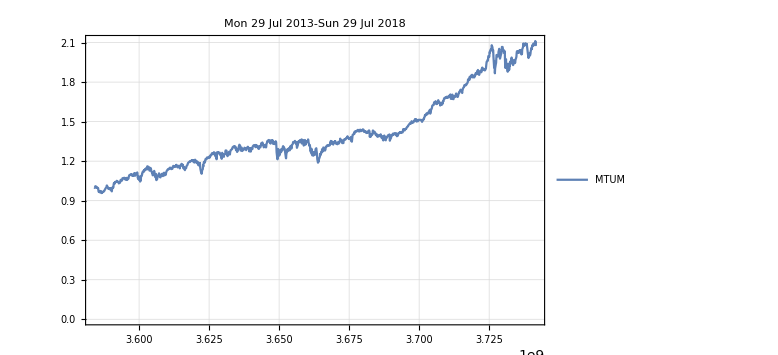
-Graphics-
 | Return | Standard Deviation | Return/SD
MTUM | 2.07344 | 0.295128 | 7.02557

```mathematica
fundChart=FinancialChart[{"MTUM"},start,end]
Export[FileNameJoin[{NotebookDirectory[],"fundChart.svg"}],fundChart];
```

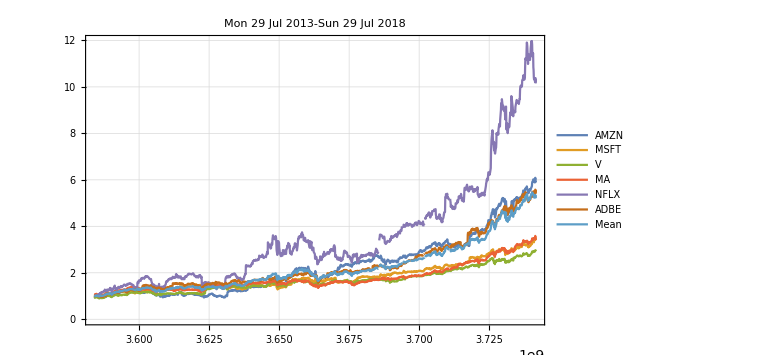
-Graphics-
 | Return | Standard Deviation | Return/SD
AMZN | 5.93685 | 1.28334 | 4.6261
MSFT | 3.41408 | 0.589292 | 5.79353
V | 2.93192 | 0.498502 | 5.88145
MA | 3.39922 | 0.577349 | 5.88763
NFLX | 10.1505 | 2.38485 | 4.25625
ADBE | 5.40195 | 1.11533 | 4.84336
Mean | 5.20575 | 1.06404 | 4.89243

```mathematica
(*weights={5.5,5.42,4.96,4.77,4.55,4.38,3.69,3.49,3.37,2.99};
symbols={"AMZN","MSFT","V","BA","MA","JPM","CSCO","INTC","NFLX","ADBE"};*)
FinancialChart[{"AMZN","MSFT","V","MA","NFLX","ADBE"},start,end]
```

```mathematica
PortfolioChart[stocks_,start_,end_]:=Module[{s,mean,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
mean=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{mean};
symbols=stocks~Join~{"mean"};
std=StandardDeviation@mean[[All,2]];
return=Last@mean[[All,2]];
TableForm@{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],{return,std,return/std}//TableForm[#,TableHeadings->{{"Return","SD","Return/SD"},Automatic}]&}
]
```

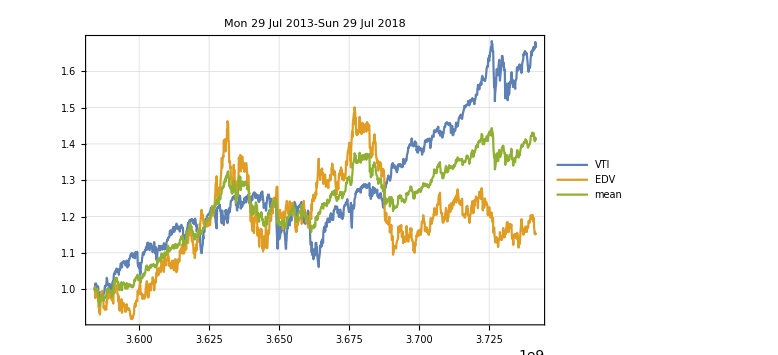
-Graphics-
Return | 1.40959
SD | 0.119416
Return/SD | 11.804

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
```